# Example of ODE solution in Mathematica

## Here we layout the basic input functions that are needed to solve a high-altitude ballastic missile problem.

```mathematica
(* Set up constants*)
Off[General::spell1];
cd := 0.1;
xarea = 0.01;  (* meters squared *)
mass = 500; (* kg *)
targdist = 100000; terr=1; (* kn *)
ltheta = Pi/4;
(* Define the acceleration functions we will need
Gravity here depends on height (x-coordinate) *)
grav[z_] := -9.806 + 3.0786 10^(-6) z;
(* Drag also depends on height becuase the air density decreases with height *)
dragz[cd_, xd_,zd_,z_] := -(1.29*Exp[-z/(7500. 10^6)]*Sqrt[xd^2+zd^2]*zd*cd*xarea)/(2 mass);
dragx[cd_, xd_,zd_,z_] := -(1.29*Exp[-z/(7500. 10^6)]*Sqrt[xd^2+zd^2]*xd*cd*xarea)/(2 mass);
Print["Default Values Set"]
```

Default Values Set

## Here we now allow user input of values

```mathematica
(* Get User inputs: Cell maybe skipped if defaults to be used*)
targdist = Input["Target Dist (km)"]*1000;
terr = Input["Error limit (m)"];
ltheta = Input["Launch Angle (deg)"]*Pi/180;
mass = Input["Body Mass (kg)"];
xarea = Input["Cross Sectional Area (m^2)"];
cd = Input["Drag coefficient"];
Print["User Values Set"]
```

## Compute an approximate solution based on analytic solution with no drag and constant g. Here we also compute analytically the change in velocity needed to move an extra distance.

```mathematica
vx = Sqrt[-targdist*grav[0]/(2*Tan[ltheta])];
dvxdD = Sqrt[-grav[0]/(2*Tan[ltheta]*targdist)]/2;
lvel = vx/Cos[ltheta];
dvdD = dvxdD /Cos[ltheta];
vz = lvel*Sin[ltheta];
Print["Initial Velocity ",lvel," m/sec, dvdD ",dvdD," (m/s)/m"]
```

Initial Velocity 990.252 m/sec, dvdD 0.00495126 (m/s)/m

## Now run the solution iteratively until target distance is reached

```mathematica
(* Set up differential equations to be be solved, x[t] is horizontal position, z[t] is height of object *)
Print["Solving with cd ",cd]
notthere = True;
While[ notthere ,
solution = NDSolve[{z''[t]==grav[z[t]]+dragz[cd, x'[t],z'[t],z[t]],
x''[t] == dragx[cd, x'[t],z'[t],z[t]],
x[0] == 0, z[0] == 0, 
x'[0] == vx, z'[0] == vz},{x,z},{t,0,1000}];
hz[t_]:= Evaluate[z[t]/.solution];
hx[t_]:= Evaluate[x[t]/.solution];
(* Compute the error in the distance *)
zerot  = t /. FindRoot[hz[t]==0 ,{t,20,500}];
derr = targdist - First[hx[zerot]];
If[ Abs[derr] > terr , 
   lvel = lvel + derr*dvdD; vx = lvel*Cos[ltheta]; vz = lvel*Sin[ltheta],
  notthere = False]
]
Print["To reach ",targdist/1000," km with Drag coefficient ",cd," and within ",terr," m"]
Print["Launch Velocity ",lvel," m/s at angle ",ltheta*180/Pi," deg"]
Print["Final position error ",terr," m"]
```

Solving with cd 0.5

To reach 100 km with Drag coefficient 0.5 and within 1 m

Launch Velocity 1323.55 m/s at angle 45 deg

Final position error 1 m

## Now plot the results.

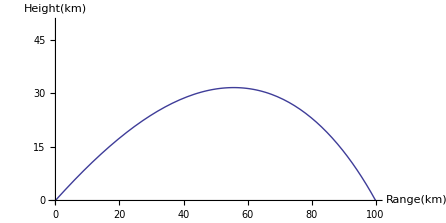

```mathematica
ParametricPlot[{First[hx[t]]/1000,First[hz[t]]/1000},{t,0,zerot},AxesLabel->{"Range(km)","Height(km)"},BaseStyle->{FontSize->12},PlotRange->{{0,100},{0,50}}]
```

## Here we can change the drag coefficent and see what happens

```mathematica
cd:=0.5;
```

```mathematica
Manipulate[Plot[Evaluate[z[t]/.First[NDSolve[{z''[t]==grav[z[t]]+dragz[cd, x'[t],z'[t],z[t]],
x''[t] == dragx[cd, x'[t],z'[t],z[t]],
x[0] == 0, z[0] == 0, 
x'[0] == vx, z'[0] == vz},{x,z},{t,0,1000}]]],{t,0,200},AxesLabel->{"Time (seconds)","Height(m)"},BaseStyle->{FontSize->12}],
{cd,0,3}]
```

```mathematica
First[hz[10]]
```

8509.98